```mathematica
itinerary[func_,x0_,n_]:=Module[{a,hor,vert},hor[{x_,y_}]:={y,y};vert[{x_,y_}]:={x,func[x]};
a[1]={x0,x0};a[k_]:=If[EvenQ[k],hor[a[k-1]],vert[a[k-1]]];
Table[a[k],{k,1,2*n}]]
singpert[x_,c_,beta_]:=x^2+c+beta/x^2
mysols=Solve[singpert[x,cval,.001]==x,x][[4]];
Manipulate[
Fp=x/.(mysols/.cval->c);
If[!NumericQ[Fp]||Im[Fp]≠0,Fp=0];
p=Plot[{x,singpert[x,c,.001](*,.001^(.25),-.001^(.25)*) },{x,-xrange,xrange},
Epilog->{Arrowheads[.025],Thick,Arrow[ itinerary[(singpert[#,c,.001])&,.001^(.25),n+1]],(*Arrow[ itinerary[(singpert[#,c,.001])&,x0,n2+1]], *)
	Thin, Red,Dashed, Line[{{{.001^(.25),-10},{.001^(.25),10}},
	{{-.001^(.25),-10},{-.001^(.25),10}},
	{{Fp,-10},{Fp,10}}
	(*{{-10,Fp},{10,Fp}}*)
}]},PlotRange->{{-xrange, xrange},{ymin, ymax}},(*ImagePadding->{{25,10},{10,10}},*) ImageSize->800, AspectRatio->x0, ImageSize->Full];
(*Button["Export",Export["~/Thesis/plot"<>ToString[c]<>".pdf",p]]*)Show[p]
,{{c,-.092495,"param"},-2,.3,stepsize,ImageSize->Small,Appearance->"Labeled",ControlPlacement->Left},
{{n,1,"iterates"},1,100,1,ImageSize->Small,Appearance->"Labeled",ControlPlacement->Left},
{{x0,.7,"aspect ratio"},-2,2,stepsize,ImageSize->Small,Appearance->"Labeled",ControlPlacement->Left},
{{zoom,.112,"zoom"},.01,.5,.001,ImageSize->Small,ControlPlacement->Left},
{{xrange,1.3,"x range"},-10,10,.1,ImageSize->Small,ControlPlacement->Left},
{{ymin,-1,"ymin"},-10,10,.1,ImageSize->Small,ControlPlacement->Left},
{{ymax,1.5,"ymax"},-10,10,.1,ImageSize->Small,ControlPlacement->Left},
 {{stepsize,.001,"Step Size"},0,1,.0001,ImageSize->Small,ControlPlacement->Left},SaveDefinitions->True,TrackedSymbols->Manipulate]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
func[x_]:=.5x;
Manipulate[
p2=Plot[{x,func[x](*,.001^(.25),-.001^(.25)*) },{x,-xrange,xrange},
Epilog->{Arrowheads[.025],Thick,Arrow[itinerary[(func[#])&,8,n+1]]},PlotRange->{{-xrange, xrange},{ymin, ymax}},(*ImagePadding->{{25,10},{10,10}},*) ImageSize->800, AspectRatio->x0, ImageSize->Full,Ticks->{{-8,-6,-4,-2,-1,1,2,4,6,8},Automatic}];
Button["Export",Export["~/Thesis/plot"<>ToString[c]<>".pdf",p2]]Show[p2]
,{{c,-.092495,"param"},-2,.3,stepsize,ImageSize->Small,Appearance->"Labeled",ControlPlacement->Left},
{{n,1,"iterates"},1,100,1,ImageSize->Small,Appearance->"Labeled",ControlPlacement->Left},
{{x0,1,"aspect ratio"},-2,2,stepsize,ImageSize->Small,Appearance->"Labeled",ControlPlacement->Left},
{{zoom,.112,"zoom"},.01,.5,.001,ImageSize->Small,ControlPlacement->Left},
{{xrange,10,"x range"},-10,10,.1,ImageSize->Small,ControlPlacement->Left},
{{ymin,-10,"ymin"},-10,10,.1,ImageSize->Small,ControlPlacement->Left},
{{ymax,10,"ymax"},-10,10,.1,ImageSize->Small,ControlPlacement->Left},
 {{stepsize,.001,"Step Size"},0,1,.0001,ImageSize->Small,ControlPlacement->Left},SaveDefinitions->True,TrackedSymbols->Manipulate]
```

```mathematica
func3[x_]:=x^2+c;
Manipulate[
p3=Plot[{x,func3[x](*,.001^(.25),-.001^(.25)*) },{x,-xrange,xrange},
Epilog->{Arrowheads[.025],Thick,Arrow[itinerary[(func3[#])&,0,n+1]]},PlotRange->{{-xrange, xrange},{ymin, ymax}},(*ImagePadding->{{25,10},{10,10}},*) ImageSize->800, AspectRatio->x0, ImageSize->Full,Ticks->{{-8,-6,-4,-2,-1,1,2,4,6,8},Automatic}];
Button["Export",Export["~/Thesis/plot3_"<>ToString[c]<>".pdf",p3]]Show[p3]
,{{c,-.092495,"param"},-2,.3,stepsize,ImageSize->Small,Appearance->"Labeled",ControlPlacement->Left},
{{n,1,"iterates"},1,100,1,ImageSize->Small,Appearance->"Labeled",ControlPlacement->Left},
{{x0,1,"aspect ratio"},-2,2,stepsize,ImageSize->Small,Appearance->"Labeled",ControlPlacement->Left},
{{zoom,.112,"zoom"},.01,.5,.001,ImageSize->Small,ControlPlacement->Left},
{{xrange,10,"x range"},-10,10,.1,ImageSize->Small,ControlPlacement->Left},
{{ymin,-10,"ymin"},-10,10,.1,ImageSize->Small,ControlPlacement->Left},
{{ymax,10,"ymax"},-10,10,.1,ImageSize->Small,ControlPlacement->Left},
 {{stepsize,.001,"Step Size"},0,1,.0001,ImageSize->Small,ControlPlacement->Left},SaveDefinitions->True,TrackedSymbols->Manipulate]
```

```mathematica
singpert
```

singpert

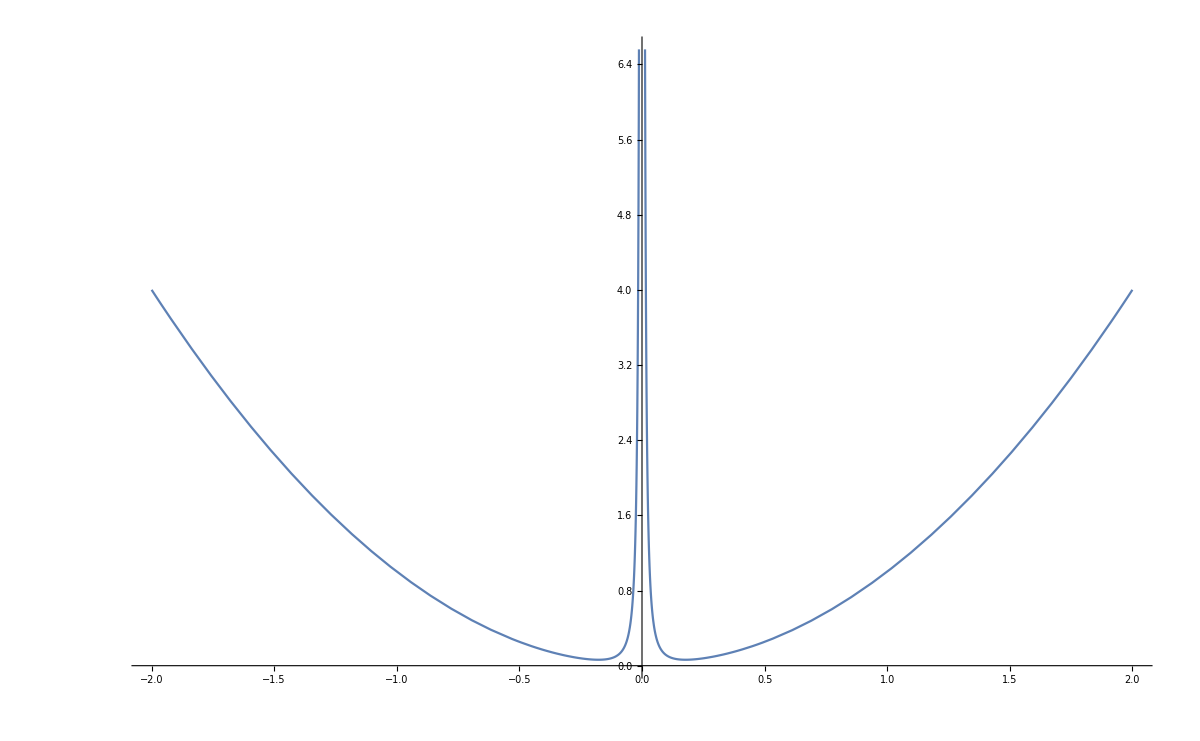

```mathematica
oot=Plot[singpert[x,0,.001],{x,-2,2},ImageSize->1200]
```